```mathematica
Clear["Global`*"]
```

```mathematica
dim=1;
R=1;
δ=1/10.;
```

```mathematica
NDSolve[{(1-2*Y[r])*D[Y[r],r]==(δ/r^(dim-1))(D[r^(dim-1)*D[Y[r],r],r]),Y[0]==1, Y[Infinity]==0},Y,r]
```

NDSolve::ndsv: Cannot find starting value for the variable Y'.

NDSolve[{(1-2 Y[r]) Y'[r]==0.1 Y''[r],Y[0]==1,Y[∞]==0},Y,r]

```mathematica
(*weqn=D[u[r,t],{t,1}]+D[u[r,t]*(1-u[r,t]),{r,1}]==(1/r^(dim-1))D[r^(dim-1)*D[u[r,t],{r,1}],{r,1}];
ic={u[r,0]== 0.5*(1-Tanh[(r-R)/δ])};
sol=DSolve[{weqn,ic},u,{r,t}]*)
```

```mathematica
(*Plot3D[Evaluate[u[x,t]/.sol[[1]]],{x,-7,7},{t,0,4},PlotRange->All]*)
```

```mathematica
(*Manipulate[Plot[Evaluate[u[x,t]/.sol[[1]]],{x,-15,15},PlotRange->All], {t,0,10}]*)
```

-(Sech[(-R+r1)/(2 δ)]^2 (δ-dim δ+2 r1 Tanh[(-R+r1)/(2 δ)]))/(4 r1 δ)

-Sech[(-R+r1)/(2 δ)]^2/(4 δ)

(Sech[(-R+r1)/(2 δ)]^2 Tanh[(-R+r1)/(2 δ)])/(4 δ^2)

-((-2+Cosh[(R-r1)/δ]) Sech[(R-r1)/(2 δ)]^4)/(8 δ^3)

-Graphics-

-Graphics-

0

Sech[(-R+r1)/(2 δ)]^2/(4 δ)

-Graphics-

-Graphics-

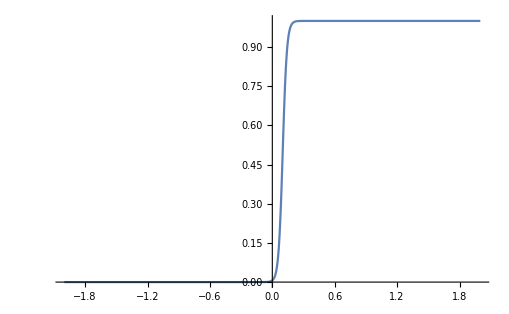

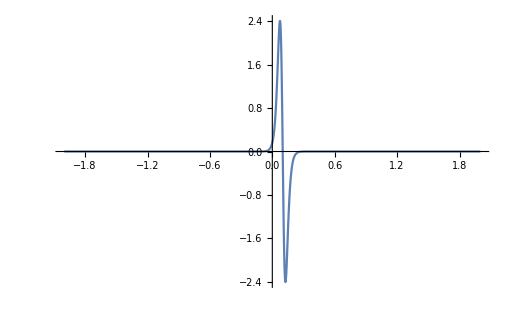

```mathematica
check[u_,r_]:=(D[u[r2]*(1-u[r2]),r2]-(1/r2^(dim-1))D[δ*r2^(dim-1)*D[u[r2],r2],r2])/.r2->r(*//Simplify*)
(*ue[r1_]:=(1/2)*(1+Tanh[(r1-R)/(2δ)]);*)
ue[r1_]:=(1/2)*(1-Tanh[(r1-R)/(2δ)]);

check[ue,r1]//Simplify
D[ue[r1],r1]
D[ue[r1],{r1,2}]
D[ue[r1],{r1,3}]//Simplify
Plot[{ue[r1], 1/(Exp[(R-r1)/δ]+1)},{r1,0,2},PlotRange->All]
Plot[{check[ue,r1]},{r1,-2,2}, PlotRange->All]
```

```mathematica
D[Tanh[x],x]
```

Sech[x]^2

```mathematica
D[ue[r1],{r1,1}]
```

-(Sech[(-R+Abs[r1])/(4 δ)]^2 Abs'[r1])/(8 δ)

```mathematica
ue[r1]
```

1/2 (1-a Tanh[(-R+Abs[r1])/(4 δ)])

```mathematica
Abs''[r1]=0;
check[ue,r1]//Simplify
```

-(Sech[(R-Abs[r1])/(4 δ)]^2 Tanh[(-R+Abs[r1])/(4 δ)] Abs'[r1] (2+Abs'[r1]))/(16 δ)

```mathematica
-(Sech[(R-Abs[r1])/(4 δ)]^2 (2 Tanh[(-R+Abs[r1])/(4 δ)] Abs'[r1]+Tanh[(-R+Abs[r1])/(4 δ)] Abs'[r1]^2-2 δ Abs''[r1]))/(16 δ)
```

-(Sech[(R-Abs[r1])/(4 δ)]^2 (2 Tanh[(-R+Abs[r1])/(4 δ)] Abs'[r1]+Tanh[(-R+Abs[r1])/(4 δ)] Abs'[r1]^2-2 δ Abs''[r1]))/(16 δ)

```mathematica
gen[r1_]:=(1/2)*(1+a*Tanh[(r1-b)/(c)]);
dgen[r_]:=D[gen[r1],{r1,1}]/.r1->r;
d2gen[r_]:=D[gen[r1],{r1,2}]/.r1->r;
gen[r]
dgen[r]
d2gen[r]
(1-2gen[r])*dgen[r]-δ*d2gen[r]//Simplify
check[gen,r1]//Simplify
```

1/2 (1+a Tanh[(-b+r)/c])

(a Sech[(-b+r)/c]^2)/(2 c)

-(a Sech[(-b+r)/c]^2 Tanh[(-b+r)/c])/c^2

-(a (a c-2 δ) Sech[(-b+r)/c]^2 Tanh[(-b+r)/c])/(2 c^2)

(a (a c-2 δ) Sech[(b-r1)/c]^2 Tanh[(b-r1)/c])/(2 c^2)

(a Sech[(-b+r)/c]^2)/(2 c)

```mathematica
Sech[5.-50. Abs[r1]]^2 (-0.25 0[r1]+Sign[r1] (-25.+25. Sign[r1]) Tanh[50. (-0.1+Abs[r1])])/.r1->1
```

3.27761×10^-39 (0.-0.25 0[1])

```mathematica
s=NDSolve[{y'[x]==y[x]Cos[x+y[x]],y[0]==1},y,{x,0,30}]
```

{{y→InterpolatingFunction[{{0., 30.}}, <>]}}

{{Y→InterpolatingFunction[{{0.0001, 3.}}, <>]}}

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.001}

InterpolatingFunction::dmval: Input value {0.0000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

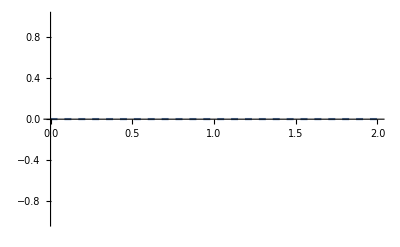

```mathematica
a=0.0001;
b=3;
dim=2;
sol=NDSolve[{(1-2*Y[r])*Y'[r]==δ*(((dim-1)/r)*Y'[r]+Y''[r]),Y[a]==0.001, Y'[a]==0},Y,{r,a,b},Method->"ImplicitRungeKutta"]
Evaluate[Y[0]/.sol]
(*sol=NDSolve[{(1-2*Y[r])*Y'[r]==δ*(Y''[r]),Y[a]==0, Y[1]==1/2},Y,{r,a,b}]*)
(*Plot[{Evaluate[Y[r]/.sol],ue[r]},{r,0,2},PlotRange->{0,1},PlotStyle->{Dashed,Dotted},PlotLegends->"Expressions"]*)
Plot[{Evaluate[Y[r]/.sol]},{r,0,2},PlotRange->{-1,1},PlotStyle->{Dashed},PlotLegends->"Expressions"]
```